# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries-split

```mathematica
dataset="omicron-countries-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
variantLabels={"other","Delta","Omicron BA.1","Omicron BA.2"};
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variantLabels[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-11-01

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-14

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-14

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{Australia,Austria,Canada,Croatia,Denmark,France,Germany,India,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{Australia,Austria,Canada,Croatia,Denmark,France,Germany,India,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.005];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;4]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

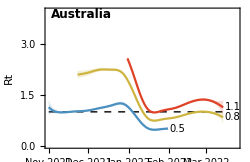
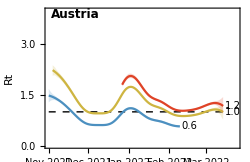
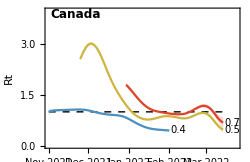
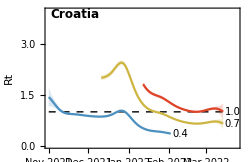
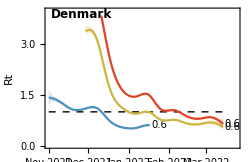
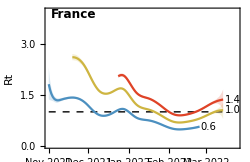
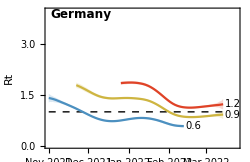
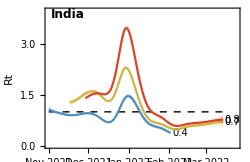
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron 21L"][[-1,1]],Round[rtGather[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-03-14,1.1,0.9,1.4},Austria→{2022-03-14,1.2,0.9,1.4},Canada→{2022-03-14,0.7,0.5,0.8},Croatia→{2022-03-14,1.,0.7,1.3},Denmark→{2022-03-14,0.6,0.5,0.8},France→{2022-03-14,1.4,1.1,1.7},Germany→{2022-03-14,1.2,1.1,1.4},India→{2022-03-14,0.8,0.6,0.9},Israel→{2022-03-14,1.1,0.8,1.3},Japan→{2022-03-14,1.1,0.8,1.3},Lithuania→{2022-03-14,0.9,0.8,1.1},Netherlands→{2022-03-14,0.5,0.4,0.7},New Zealand→{2022-03-14,1.3,0.9,1.6},Norway→{2022-03-14,0.8,0.6,1.},Singapore→{2022-03-14,0.7,0.5,0.9},Slovakia→{2022-03-14,1.,0.9,1.2},South Africa→{2022-03-14,1.,0.7,1.2},South Korea→{2022-03-14,1.4,1.2,1.5},Spain→{2022-03-14,1.2,1.,1.4},Sweden→{2022-03-14,0.9,0.5,1.4},Switzerland→{2022-03-14,1.1,0.9,1.2},Thailand→{2022-03-14,1.1,0.9,1.2},United Kingdom→{2022-03-14,1.1,0.9,1.3},USA→{2022-03-14,1.1,0.9,1.2}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.005];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,16]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;4]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

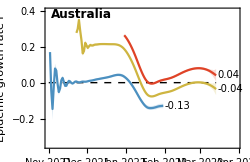
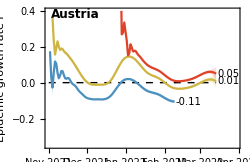
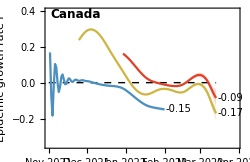
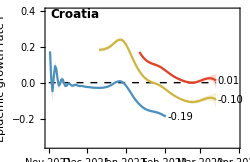
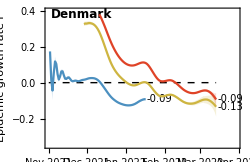
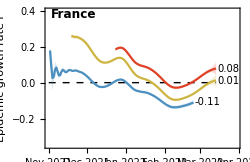
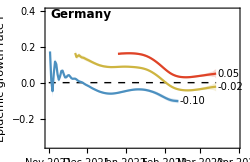
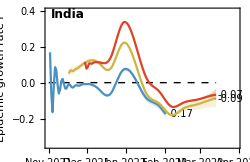
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[rGather[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-03-14,0.04,0.01,0.08},Austria→{2022-03-14,0.05,0.01,0.09},Canada→{2022-03-14,-0.09,-0.13,-0.04},Croatia→{2022-03-14,0.01,-0.03,0.05},Denmark→{2022-03-14,-0.09,-0.13,-0.06},France→{2022-03-14,0.08,0.04,0.11},Germany→{2022-03-14,0.05,0.02,0.07},India→{2022-03-14,-0.07,-0.1,-0.03},Israel→{2022-03-14,0.02,-0.02,0.05},Japan→{2022-03-14,0.01,-0.03,0.05},Lithuania→{2022-03-14,-0.01,-0.04,0.01},Netherlands→{2022-03-14,-0.12,-0.17,-0.07},New Zealand→{2022-03-14,0.04,0.,0.09},Norway→{2022-03-14,-0.06,-0.1,-0.03},Singapore→{2022-03-14,-0.07,-0.11,-0.02},Slovakia→{2022-03-14,0.01,-0.02,0.03},South Africa→{2022-03-14,-0.01,-0.05,0.03},South Korea→{2022-03-14,0.08,0.07,0.1},Spain→{2022-03-14,0.05,0.01,0.08},Sweden→{2022-03-14,-0.01,-0.09,0.07},Switzerland→{2022-03-14,0.02,-0.01,0.05},Thailand→{2022-03-14,0.02,-0.01,0.05},United Kingdom→{2022-03-14,0.04,0.01,0.06},USA→{2022-03-14,0.02,-0.02,0.05}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[Log[2]/rGather[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-03-14,17.3,9.2,102.8},Austria→{2022-03-14,14.,8.,50.4},Canada→{2022-03-14,-8.1,-17.8,-5.3},Croatia→{2022-03-14,63.4,13.8,-22.2},Denmark→{2022-03-14,-7.4,-11.9,-5.4},France→{2022-03-14,8.8,6.1,17.4},Germany→{2022-03-14,13.7,9.5,29.8},India→{2022-03-14,-10.3,-20.9,-6.9},Israel→{2022-03-14,41.7,12.8,-32.5},Japan→{2022-03-14,55.6,13.3,-26.4},Lithuania→{2022-03-14,-47.2,56.,-16.1},Netherlands→{2022-03-14,-5.9,-10.2,-4.1},New Zealand→{2022-03-14,17.9,7.9,-172.2},Norway→{2022-03-14,-10.8,-22.6,-7.1},Singapore→{2022-03-14,-10.2,-35.,-6.2},Slovakia→{2022-03-14,78.9,20.4,-37.7},South Africa→{2022-03-14,-72.4,23.9,-14.7},South Korea→{2022-03-14,8.3,6.9,10.5},Spain→{2022-03-14,15.1,8.5,60.},Sweden→{2022-03-14,-53.8,9.6,-7.7},Switzerland→{2022-03-14,28.1,12.6,-76.},Thailand→{2022-03-14,38.4,15.2,-70.4},United Kingdom→{2022-03-14,19.1,10.7,114.6},USA→{2022-03-14,34.2,13.,-42.3}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{62,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1020000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

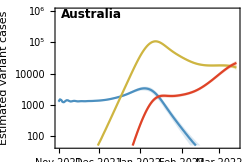
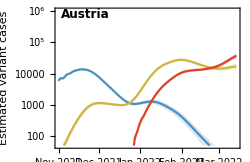
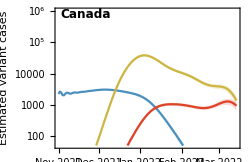
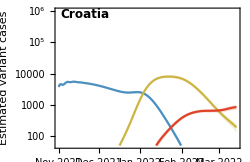
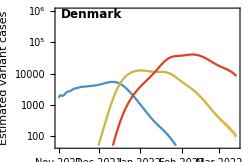
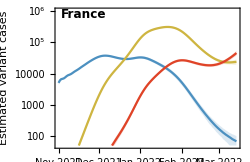
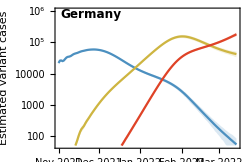
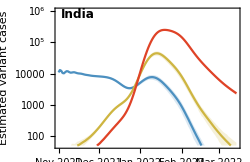
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

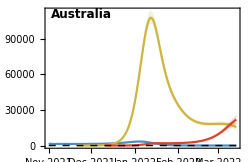
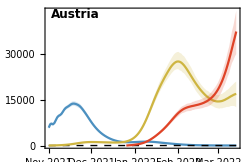
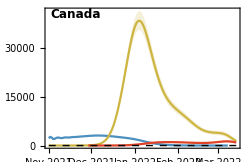
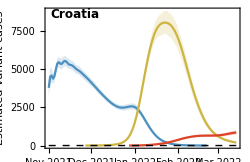
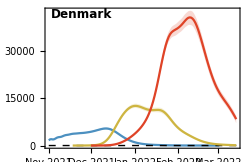
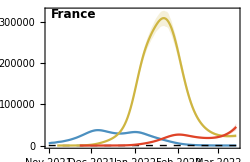
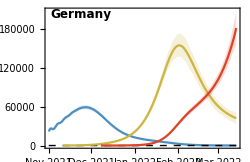
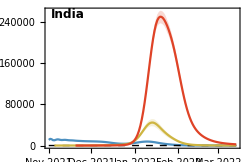
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron 21L"][[-1,1]],Round[pGather[#,"Omicron 21L"][[-1,2]]],Round[pGatherLower[#,"Omicron 21L"][[-1,2]]],Round[pGatherUpper[#,"Omicron 21L"][[-1,2]]]}&,countries]
```

{Australia→{2022-03-14,21900,17619,25866},Austria→{2022-03-14,37231,29865,44002},Canada→{2022-03-14,936,627,1205},Croatia→{2022-03-14,849,680,1004},Denmark→{2022-03-14,8406,7129,9459},France→{2022-03-14,45431,37645,53785},Germany→{2022-03-14,181163,156247,207773},India→{2022-03-14,2338,2011,2618},Israel→{2022-03-14,4156,3480,4941},Japan→{2022-03-14,10270,8514,12012},Lithuania→{2022-03-14,3892,3342,4442},Netherlands→{2022-03-14,39453,32791,46286},New Zealand→{2022-03-14,10919,8167,13772},Norway→{2022-03-14,4484,3805,5193},Singapore→{2022-03-14,10201,8647,11803},Slovakia→{2022-03-14,10024,7787,12345},South Africa→{2022-03-14,1211,1003,1403},South Korea→{2022-03-14,301471,279008,326650},Spain→{2022-03-14,16562,13504,19694},Sweden→{2022-03-14,1274,885,1601},Switzerland→{2022-03-14,26605,22493,31561},Thailand→{2022-03-14,12919,10889,15007},United Kingdom→{2022-03-14,65938,57343,73100},USA→{2022-03-14,13960,10773,16626}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

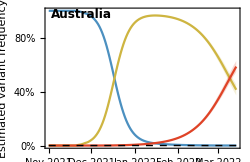
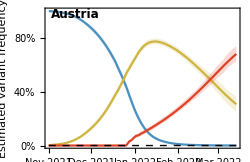
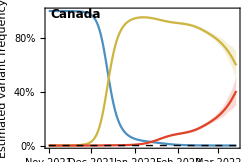
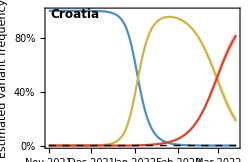
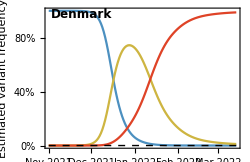
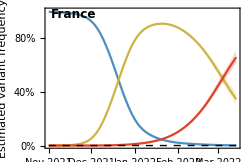
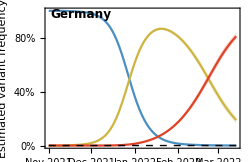
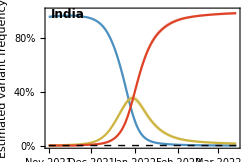
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron 21L"][[-1,1]],Round[fGather[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-03-14,0.59,0.55,0.63},Austria→{2022-03-14,0.68,0.62,0.74},Canada→{2022-03-14,0.4,0.3,0.51},Croatia→{2022-03-14,0.82,0.78,0.85},Denmark→{2022-03-14,0.99,0.98,0.99},France→{2022-03-14,0.66,0.61,0.71},Germany→{2022-03-14,0.81,0.79,0.84},India→{2022-03-14,0.98,0.97,0.99},Israel→{2022-03-14,0.74,0.7,0.77},Japan→{2022-03-14,0.19,0.17,0.22},Lithuania→{2022-03-14,0.91,0.89,0.93},Netherlands→{2022-03-14,0.82,0.8,0.84},New Zealand→{2022-03-14,0.57,0.51,0.63},Norway→{2022-03-14,0.93,0.92,0.94},Singapore→{2022-03-14,0.83,0.79,0.86},Slovakia→{2022-03-14,0.76,0.72,0.8},South Africa→{2022-03-14,0.98,0.97,0.99},South Korea→{2022-03-14,0.73,0.71,0.76},Spain→{2022-03-14,0.79,0.75,0.82},Sweden→{2022-03-14,0.96,0.96,0.97},Switzerland→{2022-03-14,0.85,0.83,0.86},Thailand→{2022-03-14,0.62,0.56,0.68},United Kingdom→{2022-03-14,0.92,0.9,0.94},USA→{2022-03-14,0.55,0.47,0.63}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron21K,pairsOmicron21L},
pairsOmicron21K=phaseGather[country,"Omicron 21K"];
pairsOmicron21L=phaseGather[country,"Omicron 21L"];
ListLogLinearPlot[{pairsOmicron21K,{Last[pairsOmicron21K]},pairsOmicron21L,{Last[pairsOmicron21L]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]],colors[[4]],colors[[4]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

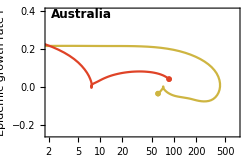
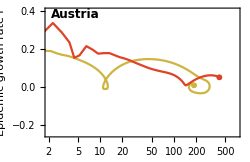
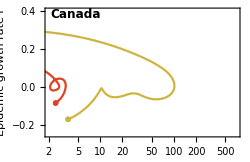
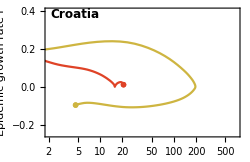
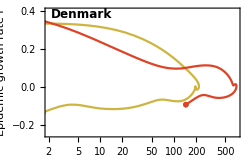
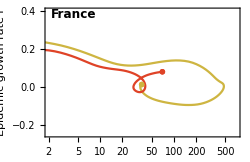
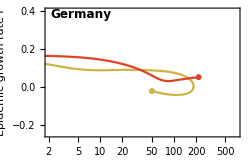
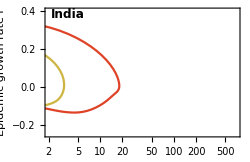
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-cases-vs-rt.png